```mathematica
playLife[state_,generationsN_: 10]:=Module[{gameOfLife},gameOfLife={224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}};
updateState=Last[CellularAutomaton[gameOfLife,#,{{0,1}}]]&;
statePlot/@NestList[updateState,state,generationsN]];
bool=#/.{True->1,False->0}&;
loob=#/.{1->True,0->False}&;
and=And@@Flatten[#]&;
statePlot::usage="statePlot[array]";
statePlot=Magnify[ArrayPlot[#,Frame->False,Mesh->True],.3]&;
lifePlot[seed_,steps_: 6]:=statePlot/@NestList[updateLife[#]&,seed,steps];
updateLife[stateXt_]:=Module[{x,xNW,xN,xNE,xW,xE,xSW,xS,xSE,xPrime,pad,dim},dim=Dimensions[stateXt];
pad=ArrayPad[#,1]&;
x[i_,j_]:=pad[stateXt][[i,j]];
xNW[i_,j_]:=x[i+1,j-1];
xN[i_,j_]:=x[i+1,j];
xNE[i_,j_]:=x[i+1,j+1];
xW[i_,j_]:=x[i,j-1];
xE[i_,j_]:=x[i,j+1];
xSW[i_,j_]:=x[i-1,j-1];
xS[i_,j_]:=x[i-1,j];
xSE[i_,j_]:=x[i-1,j+1];
xPrime[i_,j_]:=Boole[2<xNW[i,j]+xN[i,j]+xNE[i,j]+xW[i,j]+1/2 x[i,j]+xE[i,j]+xSW[i,j]+xS[i,j]+xSE[i,j]<4];Table[xPrime[i,j],{i,2,dim[[1]]+1},{j,2,dim[[2]]+1}]];

LIFE=({{0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}});
xpArray=LIFE;
(*Get["/home/asdf/Dropbox/05_PROGRAMS/001_LIFE/wordLifeDirectory/IJ2_3_GEN.m"]*)
```

```mathematica
Get[NotebookDirectory[]<>"longFORMULAmodularRECONSTRUCTED.m"]
```

```mathematica
Get[NotebookDirectory[]<>"longFORMULAmodularRECONSTRUCTED.m"];
{i,j}=Dimensions[xpArray];

Evaluate[Array[xp,{i,j}]]=loob[xpArray];
Quiet[
x1[_,0]=False;
x1[0,_]=False;
x1[_,j+1]=False;
x1[i+1,_]=False;
x0[_,0]=False;
x0[0,_]=False;
x0[_,j+1]=False;
x0[i+1,_]=False ];
```

Set::wrsym: Symbol False is Protected.

General::stop: Further output of Set::wrsym will be suppressed during this calculation.

```mathematica
beforeCNF=and@(Join[Flatten@Array[FORMULA[x1,xp],{i,j}],Flatten@Array[FORMULA[x0,x1],{i,j}]]);
MessageDialog[beforeCNF];
""
```

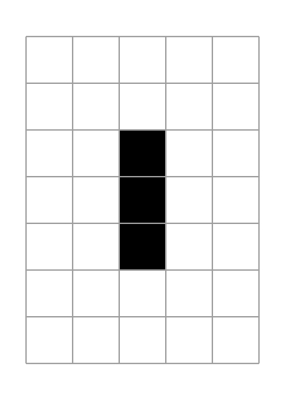
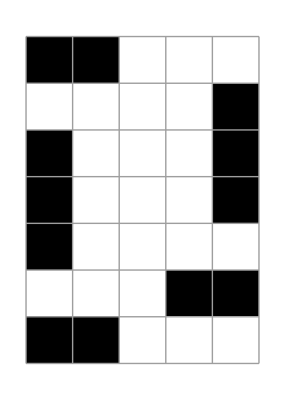
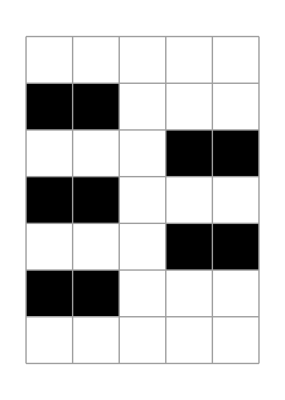
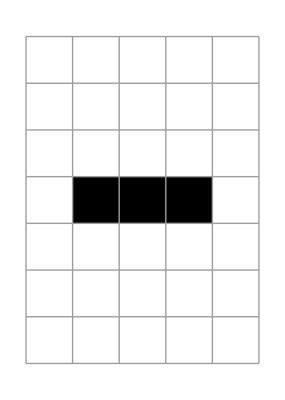
{0.055531,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
formula=beforeCNF;
STRING1="";
varlist=Join[Flatten[Array[x0,{i,j}]],Flatten[Array[x1,{i,j}]]];


asdfasdf=Row[{"sat time = ",((asdf=SatisfiabilityInstances[formula,varlist];)//AbsoluteTiming)[[1]]}];


initialState=If[Length[asdf]==0,"unsatisfiable",out1=Array[x0,{i,j}]/.Thread[varlist->RandomChoice[asdf]];
bool@out1];
AbsoluteTiming[{statePlot[LIFE],lifePlot[initialState,10]}]
```